# Normalize

## Basic Examples

```mathematica
Normalize[{1,5,1}]
```

{1/(3 √3),5/(3 √3),1/(3 √3)}

## Properties & Relations

v is a random vector:

```mathematica
v=RandomReal[{-1,1},2]
```

{-0.752333,-0.548487}

u is the normalization of v:

```mathematica
u=Normalize[v]
```

{-0.808053,-0.589109}

u is a unit vector in the direction of v:

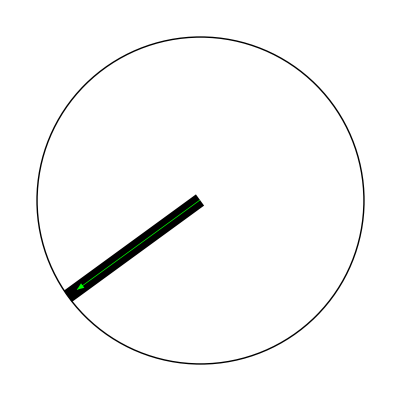

```mathematica
Show[Graphics[{Circle[{0,0},1],{Thickness[0.025],Arrow[{{0,0},u}],{Green,Thickness[0.00125],Arrow[{{0,0},v}]}}}]]
```